# An Improved, Generalized Enumeration of Substitution Systems

Kenneth E. Caviness
Camille Morrow
Christen Case
Victoria Kratzke

Physics and Engineering Department 
Southern Adventist University 
Collegedale, TN 37315 
caviness@southern.edu

The enumeration of all sequential substitution system rulesets is modified to include generalized substitution system rulesets.  Unlike its predecessor, the new enumeration is one-to-one:  each ruleset is guaranteed to appear exactly once in the new enumeration, which moreover possesses an elegant simplicity that allows jumps over increasingly longer undesired subsequences of many types.  This process effectively results in an increased acceleration and greatly improved performance.

Keywords: sequential substitution system; enumeration

Introduction

Stephen Wolfram’s ground-breaking enumeration of all elementary cellular automata was introduced as a showcase example in his book A New Kind of Science [1].  The NKS approach is to observe the behavior of a large set of “simple programs”, noticing characteristics which resemble phenomena in the natural world, perhaps ultimately providing insights about the real universe.  Critical to this method is the existence of an enumeration, which for our purposes is a well-defined way of sequentially generating all possible simple programs of the desired type.  Based on initial programs and visualizations developed by one of us [Caviness] during the 2009 NKS Summer School program in Pisa ‎[2], a complete enumeration of all rulesets of sequential substitution systems (SSSs, informally pronounced “sessies”) was developed ‎[2].  Initial use of that enumeration revealed the unsurprising result that most SSSs die out (stop changing), and most of those that do not die out are of simple, repetitive types. The human researcher must be provided with interesting cases to investigate without the need to hunt through billions of cases that die out or are functionally equivalent to ones previously studied. Therefore, it became imperative that the program do preliminary testing, and only display those of possible interest.  Of particular importance was the existence in the enumeration of long subsequences of rulesets that could all be eliminated by the same criteria, suggesting the possibility of not merely simplifying the researcher’s task, but also accelerating the iteration.  However, the complicated nature of the ranking/unranking algorithmsi caused difficulties in this effort. So while further progress on SSSs was blocked, we turned to laying the initial groundwork for the treatment of multi-way and other substitution systems, developing a more generalized enumeration.  Ironically, we found that not only does the new generalized substitution systems (GSS) enumeration allow the treatment of cases not included in the SSS enumeration, but its simple ranking/unranking functions make possible precisely calculated jumps over subsequences of unwanted cases. This feature makes it preferable for use even with SSSs.  Equally satisfactory is the fact that the new algorithm never produces the same ruleset from different indices, eliminating the 25% duplication inherent in the original SSS enumeration.  Adding in non-SSS rulesets turns out not to be a disadvantage at all!

## Substitution Systems and the Old SSS Enumeration

A sequential substitution system (SSS, pronounced “sessie”), consists of a finite length state string containing characters from an arbitrary enumerable (finite or countably infinite) alphabet, and a ruleset containing one or more rules.  Each rule consists of a pattern to search for, specified by the left-hand side of the rule, and a replacement string, given by the right-hand side.  For example, the ruleset {“AA”→”BA”, "AB”→”AA”, "B”→”AA”} contains three rules, the first of which replaces occurrences of "AA” in the state string by "BA”. The term sequential refers here to the prescribed substitution order:  The first rule is applied only at the first possible matching location in the state string, scanning from left-to-right. If no match for the first rule exists, the second rule is tried in the same way scanning the state string from left-to-right, and only if both first and second rules fail is the third used, and so on [1].  In the example above, starting with an initial state string "B”, applications of the rules successively produce the following state strings: {"B”, "AA”, "BA”, "AAA”, "BAA”, "BBA”, "AABA”, "BABA”, "BAAA”, "BBAA”, ...}.  (In this case, the rules invoked were {3, 1, 3, 1, 1, 3, 1, 2, 1, 1, ...}.)  Figure 1 is a visual representation of this SSS, showing the evolution of the state string by successive rows of colored squares (arbitrarily using gray and red to represent "A” and "B”, respectively), with the rule applied and location of each match indicated by the inset numbers.  The reader can easily confirm that each row is obtained from the previous row by applying the rule at the place shown.  Each SSS is associated with a well-defined causal network (Wolfram 1).  The SSS causal network shown in Figure 1 is the first two-dimensional network found with an internal hexagonal arrangement of nodes.

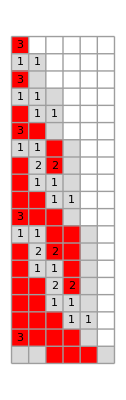
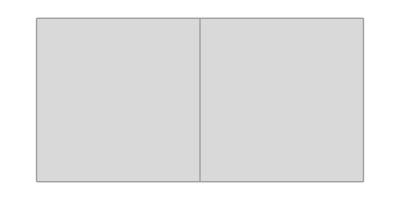



-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Figure NumberedFigure. Visual display of ruleset, early steps of evolution and casual network of a sample SSS.

If no rules apply anywhere in the state string, no further changes can occur, and the system is said to be dead.  Although we set no bound on the number of rules or string length (except that both be finite), and even the alphabet used may be countably infinite, the set of all SSS rulesets is enumerable and an enumeration was developed as detailed previously‎ (Caviness 3).  The original SSS enumeration allowed empty strings in certain positions, to accommodate deletion rules ("something”→"nothing”) anywhere, and explicitly added the possibility of a creation rule ("nothing”→"something”) at the end of the ruleset.  (This seemed natural since no rule following a creation￼ rule will ever be executed.)  Unfortunately the attempt to avoid unwanted cases resulted in an increase in the complexity and in the introduction of duplicate rulesets, with 25% of the index codes producing duplicates. Worse, in allowing deletion rules anywhere in the ruleset, the enumeration also allowed creation rules anywhere, rather than only at the end as was originally planned.  ￼It is true that adjacent￼ empty strings were only allowed at the end of the ruleset, but this turns out to be a relatively small advantage, when weighed against the enumeration’s complexity.

By moving to the generalized enumeration, we simplify the ranking/unranking functions and the calculation of jumps within the enumeration.  We allow one or at most two adjacent empty strings anywhere in the ruleset, so adjacent deletion and creation rules are possible anywhere, e.g., {"AA"→"",  ""→"A"}, but now it is a simple matter to skip an entire run of unwanted non-final creation rules in one jump.  In addition, the new enumeration can without further modification represent multi-way substitution systems (which have different criteria than SSSs).  The new algorithm is appropriately called the generalized substitution system (GSS) enumeration, as it can be used for any such system.  Its relative simplicity makes it superior to the previously used enumeration for sequential systems, and therefore the GSS enumeration can be considered a replacement for that algorithm.

## Motivation and Construction of the GSS Enumeration Algorithm

The GSS enumeration is based on a quinary (base-5) code specifying how the ruleset should be constructed by repeatedly modifying a single ruleset containing a single character "A”.  It is a consistent, logical extension of the enumeration of all lists of all strings, which is itself an extension of the universal string enumeration, using ternary and binary codes, respectively.  It is instructive to briefly review these simpler cases

To construct any string in the universal string enumeration from its index, one starts by writing the index in binary form.  The initial 1 bit is the signal to start the string with a single character "A”, and any additional bits are taken as instructions either to

0 - append an "A” to the string, or

1 - increment the final character of the string.

Thus the string is lengthened by each 0 bit to the index code, while the final character is changed to the next one in the (arbitrary) alphabet by each 1 bit.  For example, the bits of the binary number 101011 are interpreted as the instructions given in Table 1, resulting in the string "ABC”.

bit | meaning | result
1 | start    with   "A" | "A”
0 | append    an   "A" | "AA”
1 | increment   final   character | "AB”
0 | append     an   "A" | "ABA”
1 | increment   final   character | "ABB”
1 | increment   final   character | "ABC”

Any string can be formed in this way:  the process describes a bijective mapping of the positive integers onto the set of all strings.  Table 2 gives the first few strings in enumeration order, together with their indices in decimal and binary form.  It should be noted that any alphabet can be used for the characters actually making up the strings, here "ABC...” is used merely for convenience.  It is quite conceivable to use the current complete Unicode character listing, even extending it as new characters may someday be added.  Any such changes would automatically be used by our enumeration algorithm, which therefore is truly a universal list of strings, not merely of currently compiled languages but of all future human writing systems!

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1_2 | 10_2 | 11_2 | 100_2 | 101_2 | 110_2 | 111_2 | 1000_2 | 1001_2 | 1010_2
A | AA | B | AAA | AB | BA | C | AAAA | AAB | ABA

Interestingly, the initial 1 bit can be thought of as adding 2w−1 to the binary instruction code given by subsequent digits, where w is the total "weight” of the string (formed by adding the character weights:  "A”→1, "B”→2, "C”→3, etc.) and 2w−1 is simply the number of strings of weight less than w that precede all the strings of weight w, plus 1.  For example, as shown in Table 2, there are 20=1 strings of weight 1, 21=2 strings of weight 2, and 22=4 strings of weight 3.  This pattern continues: the weight of each string is the length of its binary index code, so there are 2w−1 strings of weight w. The number of strings of weight less than w is therefore 2^0+2^1+⋯+2^(w−2)=2^(w−1)−1, the sum of a finite geometric series.  We further note that within each string weight class, larger characters appear later than equivalent weight runs of smaller characters as the weight shifts toward the beginning of the string.  For example, "AAA” appears before "C”.  The reader is invited to experiment with online interactive demonstrations of this algorithm.

An enumeration of all lists of strings can be obtained by again starting with a single "A”, treating the indices as base-3 numbers, letting the three ternary digits encode the following instructions,

0 - End this string and start a new string with an "A”.

1 - Append an "A” to the last string.

2 - Increment the last character of the last string.

and then adding the ternary code to the number of smaller weight string lists, plus 1, so as to start the enumeration with index 1 rather than 0.  The interested reader is directed to [3] or [4] for details, but again lower weight string lists appear before higher weight ones, and within each weight class the weight is initially spread out (as w separate "A” strings) and is gradually compacted and shifted towards the beginning of the string.

In substitution systems it is necessary to allow empty strings (for creation or deletion rules) and even at times two adjacent empty strings, if a deletion rule is immediately followed by a creation rule, such as in {"A”→"”, "”→"A”}, for example.  This motivates the use of base-5 codes for the GSS enumeration, with the following quinary digit meanings:

0 - End this string, insert two empty strings and start a new string with an "A”.

1 - End this string, insert one empty string and start a new string with an "A”.

2 - End this string and start a new string with an "A”.

3 - End this character and start a new character (as an "A”).

4 - Increment this character.

One minor adjustment must be considered:  there are two possible rulesets of weight 1: {"”→”A”} and {"A”→””}.  To guarantee that all substitution system rulesets appear in the enumeration, simply select one of these, indicating the choice by a 0 or 1 bit, before adding the base-5 digits, giving full instructions for the construction for all weight w rulesets by the 2(5w−1) codes of the form b_1 q_2 q_3... q_w

The number of rulesets of weight less than w is

2(5^0)+2(5^1)+...+2(5^(w-2))=(2(1-5^(w-1)))/(1-5)=(5^w-5)/10

and the offset to add to the quinary code to give a unique index, starting with 1, for each ruleset of weight w
 is

(5^w-5)/10+1=(5^w-5)/10

Clearly, the useful features of the string enumeration also have their counterparts in the GSS enumeration.  Each quinary digit adds one to the weight of the ruleset (defined as the sum of the weights of its strings), so the length of the code string is by construction determined by the weight of the ruleset.  Using the proper offset for each weight class ensures that small weight rulesets appear before larger weight ones, and that each ruleset is associated with a unique index.  The enumeration includes all rulesets constructible on a finite or countably infinite alphabet, and small characters and short strings appear early the list -- a significant advantage, as we will see.  Figure 2 gives Mathematica code for the GSS rank and unrank functions, and Table 3 shows the first 75 rulesets in the GSS enumeration together with their indices.  The ordering by ruleset weight (defined as the sum of the weights of the strings in the ruleset) is clearly apparent, as is the pattern of the weight being initially as spread out as possible – single character "A" strings separated by two empty strings (the maximum allowed), and gradually being compacted and moved towards the beginning of the ruleset.  Still, many rulesets appear that are not needed for SSSs, notably cases of non-final creation rules (and even ""→"" rules), but as we will show in a later section, the underlying simplicity and coherence of enumeration allows such cases to be jumped over with little loss of time.  The most important feature is that the enumeration does not leave anything out, and any "extras" can be managed efficiently.

1 | 0_2_5 | {→A} | 23 | 0_220_5 | {→A,A→,→A} | 45 | 1_212_5 | {A→,A→A}
2 | 1_2_5 | {A→} | 24 | 0_221_5 | {→A,A→,A→} | 46 | 1_213_5 | {A→,AA→}
3 | 0_20_5 | {→A,→,A→} | 25 | 0_222_5 | {→A,A→A} | 47 | 1_214_5 | {A→,B→}
4 | 0_21_5 | {→A,→A} | 26 | 0_223_5 | {→A,AA→} | 48 | 1_220_5 | {A→A,→,A→}
5 | 0_22_5 | {→A,A→} | 27 | 0_224_5 | {→A,B→} | 49 | 1_221_5 | {A→A,→A}
6 | 0_23_5 | {→AA} | 28 | 0_230_5 | {→AA,→,A→} | 50 | 1_222_5 | {A→A,A→}
7 | 0_24_5 | {→B} | 29 | 0_231_5 | {→AA,→A} | 51 | 1_223_5 | {A→AA}
8 | 1_20_5 | {A→,→A} | 30 | 0_232_5 | {→AA,A→} | 52 | 1_224_5 | {A→B}
9 | 1_21_5 | {A→,A→} | 31 | 0_233_5 | {→AAA} | 53 | 1_230_5 | {AA→,→A}
10 | 1_22_5 | {A→A} | 32 | 0_234_5 | {→AB} | 54 | 1_231_5 | {AA→,A→}
11 | 1_23_5 | {AA→} | 33 | 0_240_5 | {→B,→,A→} | 55 | 1_232_5 | {AA→A}
12 | 1_24_5 | {B→} | 34 | 0_241_5 | {→B,→A} | 56 | 1_233_5 | {AAA→}
13 | 0_200_5 | {→A,→,A→,→A} | 35 | 0_242_5 | {→B,A→} | 57 | 1_234_5 | {AB→}
14 | 0_201_5 | {→A,→,A→,A→} | 36 | 0_243_5 | {→BA} | 58 | 1_240_5 | {B→,→A}
15 | 0_202_5 | {→A,→,A→A} | 37 | 0_244_5 | {→C} | 59 | 1_241_5 | {B→,A→}
16 | 0_203_5 | {→A,→,AA→} | 38 | 1_200_5 | {A→,→A,→,A→} | 60 | 1_242_5 | {B→A}
17 | 0_204_5 | {→A,→,B→} | 39 | 1_201_5 | {A→,→A,→A} | 61 | 1_243_5 | {BA→}
18 | 0_210_5 | {→A,→A,→,A→} | 40 | 1_202_5 | {A→,→A,A→} | 62 | 1_244_5 | {C→}
19 | 0_211_5 | {→A,→A,→A} | 41 | 1_203_5 | {A→,→AA} | 63 | 0_2000_5 | {→A,→,A→,→A,→,A→}
20 | 0_212_5 | {→A,→A,A→} | 42 | 1_204_5 | {A→,→B} | 64 | 0_2001_5 | {→A,→,A→,→A,→A}
21 | 0_213_5 | {→A,→AA} | 43 | 1_210_5 | {A→,A→,→A} | 65 | 0_2002_5 | {→A,→,A→,→A,A→}
22 | 0_214_5 | {→A,→B} | 44 | 1_211_5 | {A→,A→,A→} | 66 | 0_2003_5 | {→A,→,A→,→AA}

```mathematica
fromGeneralizedRank[i_Integer/;i>0] := Module[{n,j,bit,quinaryDigits,numberOfEOS,chopPos,ans,strings,ruleset},
n=Floor[Log[5,10i-5]];
j=i-(5^n+5)/10;
{bit,j}=QuotientRemainder[j,5^(n-1)];
quinaryDigits=IntegerDigits[j,5,n-1];
ans=Switch[bit,0,{{},{1}},1,{{1}}];
Scan[Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]];
```

```mathematica
toGeneralizedRank[rs_List] := Module[{rl,wl,w,bit,quincode=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}} && wl≠{{},{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, quincode="4"<>quincode; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  quincode="3"<>quincode; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, quincode="0"<>quincode; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, quincode="1"<>quincode; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  quincode="2"<>quincode; wl=Drop[wl,-1]
]];
Switch[wl,{{},{1}}, bit=0,{{1}} ,bit=1];
FromDigits[bit<>quincode,5]+(5^w+5)/10];
```

## The Reduced (RSS) Algorithm

The GSS enumeration includes all rulesets for general substitution systems.  It can be used equally well for the treatment of sequential substitution systems, particularly when implemented with long jumps to bypass runs of consecutive rulesets that can be omitted in the study of SSSs.  Several long-jump criteria for SSSs will be considered in the next section.  Of course, the same can be done for other types of substitution systems as well, although the criteria will differ.  But one simplification worth considering first is removing the initial binary code used to distinguish between rulesets starting with a creation rule ("”→”something”) and those that do not.  Particularly for the SSS enumeration, where the only rulesets needing consideration are those without creation rules or with one creation rule as the final rule in the ruleset, eliminating in advance all initial creation rules could be advantageous, halving the number of cases to consider.  This can be done almost trivially by dropping the initial bit of the quinary code and using the instructions to operate on the initial ruleset {"A”→"”} in all cases.  The only additional modification needed is to change the offset for weight class w rulesets to (5^(w-1)+3)/4, calculated as one more than the number of rulesets of weight less than w.

The reduced enumeration algorithm, which includes all SSS cases we might be interested in, with the exception of rulesets containing a single creation rule, {"”→"something”}, is shown in Figure 3 and the beginning of the list generated is shown in Table 4.  Long jumps over non-final creation rules will still be needed, in addition to skipping over runs of omittable rulesets of other types.  It should be noted, however, that this strategy will also remove singleton creation rules such as {"”→"A”}, which would not be excluded from the SSS case by other considerations.  But in fact all such SSS cases very closely resemble each other, and can be treated separately if desired.

1 | _5 | {A→} | 23 | 31_5 | {AA→,A→} | 45 | 023_5 | {A→,→A,AA→}
2 | 0_5 | {A→,→A} | 24 | 32_5 | {AA→A} | 46 | 024_5 | {A→,→A,B→}
3 | 1_5 | {A→,A→} | 25 | 33_5 | {AAA→} | 47 | 030_5 | {A→,→AA,→,A→}
4 | 2_5 | {A→A} | 26 | 34_5 | {AB→} | 48 | 031_5 | {A→,→AA,→A}
5 | 3_5 | {AA→} | 27 | 40_5 | {B→,→A} | 49 | 032_5 | {A→,→AA,A→}
6 | 4_5 | {B→} | 28 | 41_5 | {B→,A→} | 50 | 033_5 | {A→,→AAA}
7 | 00_5 | {A→,→A,→,A→} | 29 | 42_5 | {B→A} | 51 | 034_5 | {A→,→AB}
8 | 01_5 | {A→,→A,→A} | 30 | 43_5 | {BA→} | 52 | 040_5 | {A→,→B,→,A→}
9 | 02_5 | {A→,→A,A→} | 31 | 44_5 | {C→} | 53 | 041_5 | {A→,→B,→A}
10 | 03_5 | {A→,→AA} | 32 | 000_5 | {A→,→A,→,A→,→A} | 54 | 042_5 | {A→,→B,A→}
11 | 04_5 | {A→,→B} | 33 | 001_5 | {A→,→A,→,A→,A→} | 55 | 043_5 | {A→,→BA}
12 | 10_5 | {A→,A→,→A} | 34 | 002_5 | {A→,→A,→,A→A} | 56 | 044_5 | {A→,→C}
13 | 11_5 | {A→,A→,A→} | 35 | 003_5 | {A→,→A,→,AA→} | 57 | 100_5 | {A→,A→,→A,→,A→}
14 | 12_5 | {A→,A→A} | 36 | 004_5 | {A→,→A,→,B→} | 58 | 101_5 | {A→,A→,→A,→A}
15 | 13_5 | {A→,AA→} | 37 | 010_5 | {A→,→A,→A,→,A→} | 59 | 102_5 | {A→,A→,→A,A→}
16 | 14_5 | {A→,B→} | 38 | 011_5 | {A→,→A,→A,→A} | 60 | 103_5 | {A→,A→,→AA}
17 | 20_5 | {A→A,→,A→} | 39 | 012_5 | {A→,→A,→A,A→} | 61 | 104_5 | {A→,A→,→B}
18 | 21_5 | {A→A,→A} | 40 | 013_5 | {A→,→A,→AA} | 62 | 110_5 | {A→,A→,A→,→A}
19 | 22_5 | {A→A,A→} | 41 | 014_5 | {A→,→A,→B} | 63 | 111_5 | {A→,A→,A→,A→}
20 | 23_5 | {A→AA} | 42 | 020_5 | {A→,→A,A→,→A} | 64 | 112_5 | {A→,A→,A→A}
21 | 24_5 | {A→B} | 43 | 021_5 | {A→,→A,A→,A→} | 65 | 113_5 | {A→,A→,AA→}
22 | 30_5 | {AA→,→A} | 44 | 022_5 | {A→,→A,A→A} | 66 | 114_5 | {A→,A→,B→}

```mathematica
fromReducedRank[i_Integer/;i>0] := Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];  (* the base-5 code for this ruleset will contain n digits, the ruleset weight is n+1 *)
Scan[Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]];
```

```mathematica
toReducedRank[rs_List] := Module[{rl,wl,w,code=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, code="4"<>code; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="3"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, code="0"<>code; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="1"<>code; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  code="2"<>code; wl=Drop[wl,-1]
]];
(FromDigits[code,5]+(5^(w-1)+3)/4)  (* add number of smaller weight rulesets *) ];
```

## Criteria for Skipping SSS Rulesets and Long Jump Calculations

Even the RSS enumeration includes many rulesets that we can discard immediately.  For example, {"A”→””, "”→”A”, "”→””, "A”→””} (#7 in the RSS list, quinary code 005) would be eliminated for several reasons:  it includes an identity rule (where a string is replaced by itself) and several pairs of conflicting rules (for instance where different rules have the same left-hand side, thereby giving conflicting instructions).  Such problems, explained in detail below, guarantee that the SSS generated by this ruleset will be identical to that of a simpler one that has already appeared earlier in the enumeration.  Omitting such cases before any more time is invested greatly speeds up any treatment of SSSs.  Even more significantly, due to the nature of the enumeration algorithm, cases that would be skipped for the same reason occur consecutively, allowing us to jump past all similar cases without any testing at all.  In this section we consider the four of the most productive criteria for these "long jumps” and how the jump size can be calculated.

### Conflicting Rules

A pair of conflicting rules occurs when two rules in the ruleset have the same left-hand side, or more generally, when the left-hand side of one rule is a substring of the left-hand side of a later rule. For example, consider the ruleset {"ABA”→”AAB”, "ABA”→””, "A”→”ABA”} (# 158 448 842 380 in the RSS list, quinary code = 3432334234312343_5).



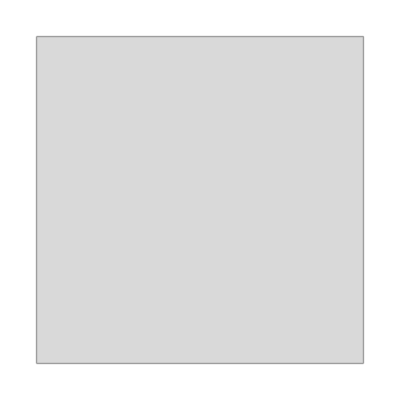
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

A conflicting rule situation ensures that some rule in the set will never be used.  In this case, whenever there is an "ABA” to be found, the first rule will be executed.  The second rule will never be invoked, since it is only considered if the first rule fails. Therefore, the ruleset is functionally equivalent a simpler ruleset that appears earlier in the enumeration: {"ABA”→”AAB”, "A”→”ABA”} (# 253 518 005 in the RSS list, quinary code = 343233422343_5).

Every conflicting rules case identified is actually one of a run of rulesets in the enumeration having the same problem.  Rather than testing each of these rulesets separately, to accelerate the enumeration we can jump directly to the last ruleset in the run of those sharing the particular problem, or to the first which does not (i.e, the resolution of the problem), either using knowledge of the enumeration or by performing an operation on the quinary code.

It is helpful to consider the first ruleset in the run of rulesets sharing the problem. For this we need to look at where the conflicting rule is located in the ruleset. A shortcut to finding the quinary code digit which caused the conflict is to add up the combined weight of the remaining characters in the ruleset after the problem. In the example above the conflicting (second) rule is "ABA”→””, but the actual problem is due to the left-hand side of this rule, "ABA”.  The remaining weight after the problem is 5, found by adding the weights of all subsequent strings in the ruleset:  "”, "A”, "ABA” (0 + 1 + 1 + 2 + 1).  The quinary code for our example above is 3432334234312343_5 and changing the rightmost five digits to 0 will result in a quinary code of the first problem ruleset in the run, the first one to start with {"ABA”→”AAB”, "ABA”→...}, followed by some distribution of strings having weight 5. Here the first problem ruleset has the quinary code of 3432334234300000_5, which translates to {"ABA”→”AAB”, "ABA”→””, "”→”A ", "”→””, "A "→””, "”→”A ", "”→””, "A "→””, "”→”A "} (# 158 448 841 407 in the RSS list).  Operating directly on the quinary code, we have truncated the final five digits and then appended five ‘0’s.  Mathematically this can be accomplished for remaining weight w by dividing the base-5 number by 5^w, discarding any remainder, then multiplying by 5^w, effectively replacing the last w digits by 0s.  Reminder: to generate the quinary code, subtract (5^(w-1)+3)/4 from the actual RSS index and then write the result as a base-5 number, where w is the weight of the ruleset, found by adding up the weights of all the characters in all the strings, or from the index i: w = IntegerPart[log_5(4i - 3)] + 1.

Once the first conflicting ruleset that shares the problem is known, the first ruleset which does not share the problem can be easily found, again by replacing the last w digits: the first by a ‘4’ and the rest by ‘0’s.  Mathematically, this means adding 4(5^(w-1)) to the RSS enumeration index of the first problem that occurs.  In this example, the first ruleset without the problem would be {"ABA”→”AAB”, "ABB”→””, "”→”A”, "”→””, "A "→””, "”→”A ", "”→””, "A "→””} (# 158 448 843 907 in the RSS list, quinary code 3432334234340000_5).  The reason this resolution ruleset no longer contains the problematic conflicting rule is because the ‘4’ incremented the last character of the string being constructed, changing the second "ABA” string to "ABB”.  Appending ‘0’s to the quinary code completes the desired weight, giving the first ruleset after the run of problematic cases.

One exception to this process is when the conflicting rules situation involves an empty string, i.e., a creation rule. An empty string in the left-hand side of any rule except the last one will automatically conflict with any rule that follows it.  The only way to avoid this situation is to have no further rules, achieved by shifting the weight of any subsequent rules into the right-hand side of the (now final) creation rule.  There are two possible cases:  (0) If the creation rule was created by a ‘0’ in the quinary code, in the resolution code the ‘0’ becomes a ‘1’ and all later digits are changed to ‘3’, effectively making the "”→ "” + weight-w rule sequence into "”→"AAA...A”, with w "A” characters.  (1) If the creation rule was created by a ‘1’, the right-hand side is not empty (and not a problem), but any additional rules’ weight must be appended to it as a string of "A” characters.  Find the combined weight w of any rules following the creation rule (past its right-hand side), and replace the last w quinary code digits by ‘3’s.

It may be noted that the normal resolution process of the first type described above (replacing the final w quinary digits by ‘4’ followed be ‘0’s) usually creates a new conflicting rules situation of the second type, which, in turn, will be resolved in the next step.

### Identity Rule

An identity rule occurs when the left-hand side of a rule is identical to the right-hand side of that same rule. A ruleset containing an identity rule and at least one other rule can be discarded, whether or not the identity rule is ever executed. For example, consider the ruleset {"A”→"CC”, "B”→"B”, "C”→"A”} (# 5 178 059 904 in RSS list, quinary code = 24434424242442_5). If the second rule is never executed, the behavior of the ruleset is equivalent to a simpler, previously considered one, without the identity rule: {"A”→"CC”, "C”→"A” } (# 8 284 904, quinary code = 2443442442_5).  On the other hand, if the identity rule is executed once, the enumeration will go into an infinite loop of "B”→"B” and any later rules will never be executed afterwards.

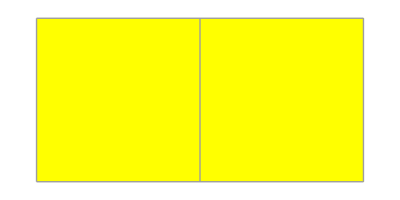
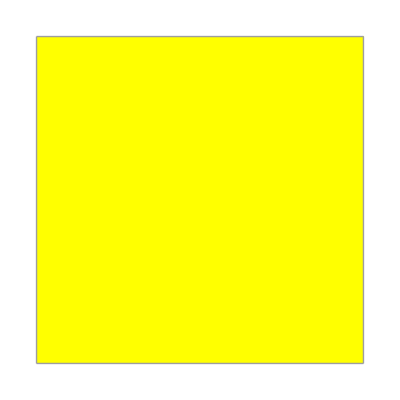
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

Again, this ruleset is part of a subsequence in the enumeration, all starting the same way and including the same identity rule. To be able to jump over them all, we must first identify where in the ruleset the problem occurs. This is done by looking at the left-hand and right-hand side of each rule and checking whether they are identical.  Then we identify which quinary code digit caused the problem, and zero out the quinary code after the problem digit to form the first ruleset with this problem. In the example above, the identity rule is followed by the strings "C” and "A”, having combined weight 3 + 1 = 4, so it was the fifth digit from the last in the quinary code 24434424242442_5 that created the "B” in the right-hand side of the identity rule "B”→"B”.  Changing the last four digits to ‘0’ gives 24434424240000_5 which corresponds to the ruleset {"A”→"CC", "B"→"B", ""→"", "A"→"", ""→"A", ""→"", "A"→""} (# 5 178 059 532 in the RSS list), the first in our run sharing the same initial rules up to and including this particular identity rule problem.

The process of finding the resolution follows a similar method. Once the identity rule is found and identified, change the digit of the quinary code directly after the one that caused the identity problem to a ‘3’ (an append instruction, which changes the current string by adding an "A" to it) and then zero out the remaining digits. In our example, we would change the quinary code 24434424242442_5 to 24434424243000_5 which corresponds to the ruleset {"A"→ "CC", "B"→"BA", ""→"", "A"→"", ""→"A", ""→"", "A"→""} (# 1 027 669 282 in the RSS list).  Again, starting with quinary code 2434424240000_5 all rulesets in the enumeration, up to but not including the resolution, 2434424243000_5, share the same first rule and the identity rule, a situation that allows a long-jump over this entire subsequence of the enumeration.

The mathematical algorithm for this process is:  truncate the last w digits of the quinary code (dividing by 5^w and taking the integer part), then multiply by 5^w, and finally add 3(5^(w-1)), where w is the weight of the strings after the identity rule.

The exception to this algorithm is when the identity rule involves two empty strings: finding the resolution in this case involves a process slightly different from the one described above. The quinary digit that created a    ""→"" identity rule is necessarily a ‘0’, and the first ruleset in the problem run can still be found by zeroing out the remaining quinary digits.  But to find the resolution we change the problem digit itself to a ‘1’ (an instruction which creates only one empty string and then starts a new string with an "A" without creating the problematic second empty string), and then filling the remaining digits by ‘0’s. Mathematically, if w is the weight of the strings after a ""→"" identity rule, we truncate the last w digits, multiply by 5^w, and finally add 1(5^(w-1)).

Note, however that a non-final ""→"" identity rule, such as shown in the last example in the table above, is also a conflicting rules situation, whose resolution takes us farther in the RSS enumeration than the identity rule resolution shown.  Here the conflicting rules resolution occurs at quinary code 2413333_5 {"A"→"B", ""→"AAAAA"}.

### Initial Substring Rule

Substring rules occur when the left-hand side of a rule contains a substring of the right-hand side of the same rule. Our concern here is when the substring rule is the first in the ruleset and is not the only rule in the ruleset. For example, consider the ruleset {"A"→"BAC", "B"→"C", "C"→"B"} (# 128 230 799 521 in the RSS list, quinary code = 2433442424424424_5).  If the first rule is ever executed it will go into an infinite loop, exhibiting behavior equivalent to the simpler ruleset {"A"→"BAC"}:  rules 2 and 3 will never be executed again. Each invocation of rule 1 replaces the first "A" in the state string by "BAC":  "A", "BAC", "BBACC", "BBBACCC", and so on.  On the other hand, if the state string has no "A", rule 1 is never invoked, and the behavior depends only on rules 2 and 3.  A simple example of this situation starts with the initial string "B":  "B", "C", "B", "C", ….

Which behavior occurs depends on the initial state string.  But in any case, a substring rule in first position in the ruleset reduces to one of two cases considered earlier in the enumeration, and so is effectively a duplication which can be discarded.  To jump over the whole run of such cases, we first identify where the problem occurs in the ruleset. In this example, the problem occurs at the character "A" on the right-hand side of the first rule ({"A"→"BAC", "B"→"C", "C"→"B"}). The quinary code which triggered the problem is the third digit, highlighted for easy reference: 2433442424424424_5.

To find the first ruleset where this particular initial substring rule occurs, we zero out the remaining digits after the highlighted problem digit. In this example, the quinary code of 2433442424424424_5 is changed to 2430000000000000_5 which corresponds to the ruleset {"A"→"BA", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"",  "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→""}.  The number of digits to zero out can be found from the weight of the post-problem (sub)string(s) in the ruleset (here: "C","B","C","C","B": 3+2+3+3+2 = 13).

To skip over to the first ruleset without this conflict, we change the next quinary code digit to a ‘4’ and zero out all digits after it. In this case, the new quinary code will be 2434000000000000_5. This gives us the new ruleset of {"A"→"BB", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A", ""→"", "A"→"", ""→"A"} (# 128 234 863 282 in the RSS list).  While this is similar to the conflicting rules situation, the quinary patterns are different enough to consider it separately.  Note particularly that in the reduced SSS enumeration, the first rule of the ruleset cannot start with an empty string, eliminating a large class of initial substring rule cases and obviating the need for separate treatment of them.   Note, however, that these cases are included in the GSS enumeration:  the last example in Table 7 is of this type.  Resolution is achieved by replacing the initial problem (binary digit ‘0’) by a ‘1’, and zeroing out the remaining quinary digits.

Note:  a substring rule not in the initial position of the ruleset does not necessarily reduce to a simpler case.  Example: {"AC"→"", "AB"→"AA", "A"→"BAC", "B"→"AA"} (#19928943753645, quinary code: 3441342322433442423_5). Rule 3 is a substring rule, but its execution does not cause an infinite loop, since rule 1, which has precedence, can also "use up" the character "A", rather than allowing rule 3 to repeat indefinitely.  Starting with an initial state string of "A" would allow all four rules to be executed according to a complicated, non-repeating pattern, yielding, successively, the state strings {"A", "BAC", "B", "AA", "BACA", "BA", "BBAC", "BB", "AAB", "AAA", "BACAA", "BAA", "BBACA", "BBA", "BBBAC", "BBB", "AABB", "AAAB", "AAAA", …}.  Unlike initial substring rule cases, rulesets with non-initial substring rules should be tested individually for possible interesting behavior.

### Renamed Ruleset

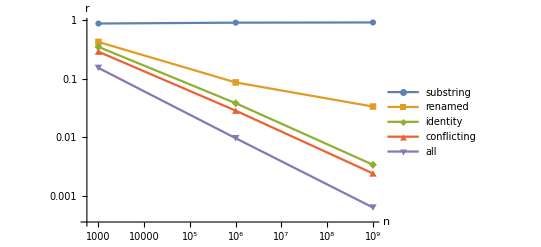

SectionAlt

Text. With NoIndent modifier style.

SubsectionAlt

Text. With NoIndent modifier style.

SubsubsectionAlt

Text. With NoIndent modifier style.

Appendix. With ProductionPageBreak Modifier Style.

AppendixSectionFirst

Text. With NoIndent modifier style.

AppendixEquation

AppendixEquation

Figure AppendixSection.FigureCaptionAppendix. FigureCaptionAppendix.

Table AppendixSection.TableCaptionAppendix. TableCaptionAppendix.

AppendixSection

Text. With NoIndent modifier style.

AppendixEquation

Text.

AppendixEquation

DisplayFormula  (use DisplayFormula for unnumbered displays in the appendix)

Figure AppendixSection.FigureCaptionAppendix. FigureCaptionAppendix.

Table AppendixSection.TableCaptionAppendix. TableCaptionAppendix.

References

Reference.

Reference.

Reference.